## DNA (ψ̂)_11 Eigenvalue Analysis

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11

0.25

10

*** Eigenvalues ***

*** Eigenvectors ***

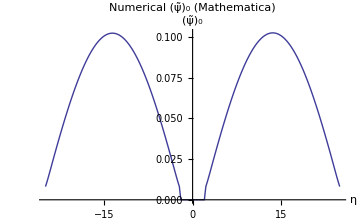

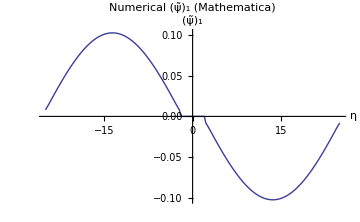

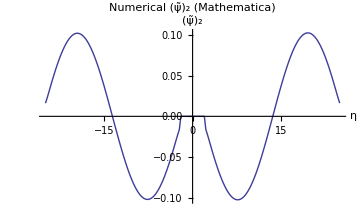

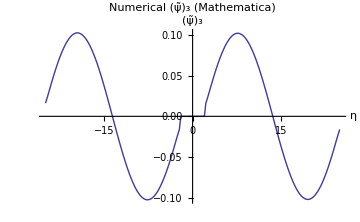

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

L=50;
m=100;
Δ=L/(2 m)//N
κ=10;
σ=1;

κσr=κ/σ

LastEval=10;

ηb=2;

max=2m+1;

(*Numerical*)
V[η_]:=If[Abs[η]≤ηb,(2 η^2)/κσr,(2 ηb^2)/κσr];

g0[η_]:=If[Abs[η]≤ηb,1,0];
g1[η_]:=If[Abs[η]≤ηb,0,1];

T[η1_,η2_] :=   g1[η1] *g1[ η2]*Exp[-(η1 - η2)^2]*Exp[-1/2(V[η1] + V[η2])];
MT = Table[Δ T[ Δ R1, Δ R2],{R1, -m, m}, {R2, -m, m}] // N;
MatrixForm[MT];

Print["*** Eigenvalues ***"]
Subscript[Mλ, t] = Eigenvalues[MT];
Print["*** Eigenvectors ***"]
Subscript[Mψ, t] = Eigenvectors[MT];

Subscript[dataMψ, 0]=Table[{Δ j,Subscript[Mψ, t][[1,j+m+1]]},{j,-m,m}];
Subscript[dataMψ, 1]=Table[{Δ j,-Subscript[Mψ, t][[2,j+m+1]]},{j,-m,m}];
Subscript[dataMψ, 2]=Table[{Δ j,-Subscript[Mψ, t][[3,j+m+1]]},{j,-m,m}];
Subscript[dataMψ, 3]=Table[{Δ j,-Subscript[Mψ, t][[4,j+m+1]]},{j,-m,m}];


(************************************************************)
Subscript[pdataMψ, 0]=ListLinePlot[Subscript[dataMψ, 0],PlotStyle->{Thick},AxesLabel -> {η,Subscript[ψ̃, 0]},PlotLabel->"Numerical (ψ̃)_0 (Mathematica)",ImageSize->Medium,PlotRange->All]
(************************************************************)
Subscript[pdataMψ, 1]=ListLinePlot[Subscript[dataMψ, 1],PlotStyle->{Thick},AxesLabel -> {η,Subscript[ψ̃, 1]},PlotLabel->"Numerical (ψ̃)_1 (Mathematica)",ImageSize->Medium,PlotRange->All]
(************************************************************)
Subscript[pdataMψ, 2]=ListLinePlot[Subscript[dataMψ, 2],PlotStyle->{Thick},AxesLabel -> {η,Subscript[ψ̃, 2]},PlotLabel->"Numerical (ψ̃)_2 (Mathematica)",ImageSize->Medium,PlotRange->All]
(************************************************************)
Subscript[pdataMψ, 3]=ListLinePlot[Subscript[dataMψ, 3],PlotStyle->{Thick},AxesLabel -> {η,Subscript[ψ̃, 3]},PlotLabel->"Numerical (ψ̃)_3 (Mathematica)",ImageSize->Medium,PlotRange->All]
(************************************************************)


fsTitle=24;
fsAxesLabel=24;
fs2=18;
```

Comparison of Eigenfunctions - Numerical and Analytical

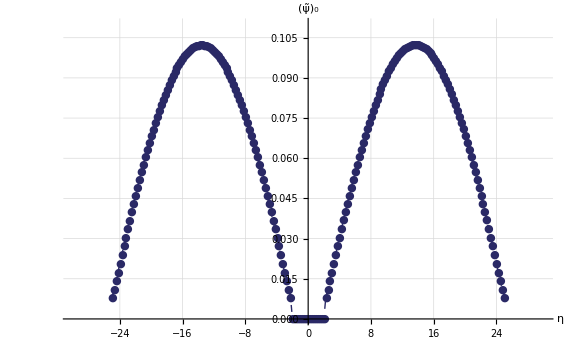

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11/0.25

0.25/psi_t11_t0_L50_m100_k10_etab2.pdf

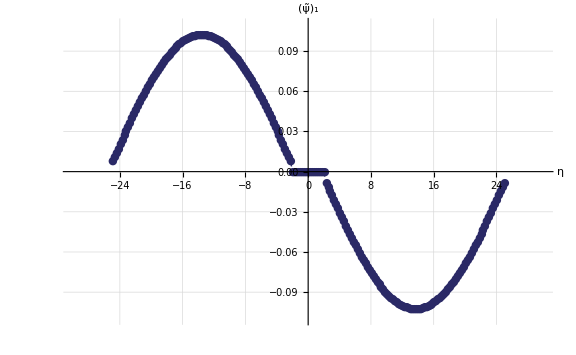

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11/0.25

0.25/psi_t11_t1_L50_m100_k10_etab2.pdf

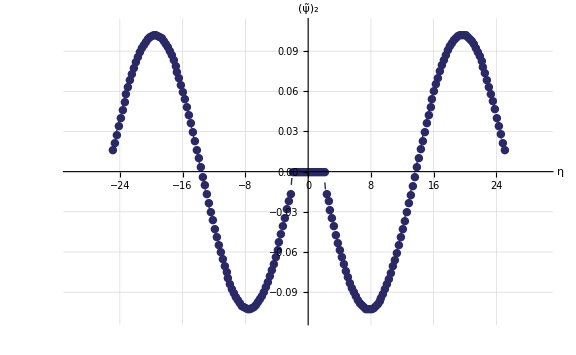

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11/0.25

0.25/psi_t11_t2_L50_m100_k10_etab2.pdf

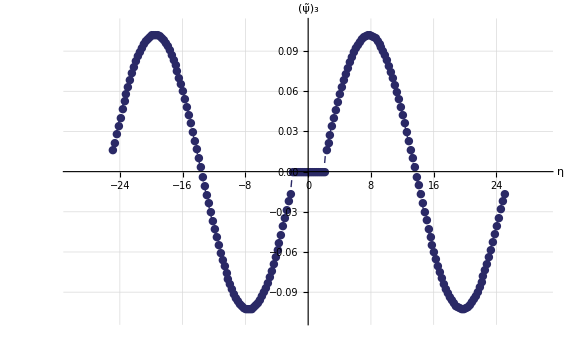

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11/0.25/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T11/0.25

0.25/psi_t11_t3_L50_m100_k10_etab2.pdf

```mathematica
xRange=30;
yRange=0.11;

t=0;
p1=ListLinePlot[Subscript[dataMψ, t],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->All];
legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fsAxesLabel]},{}};
EfunPlotψ=Show[{p1},PlotRange->{{-xRange,xRange},{0,yRange}},ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel -> {Style["η",FontSize->fsAxesLabel],Style[Subscript["ψ̃",ToString[t]],FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/psi_t11_t"<>ToString[t]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",EfunPlotψ]

t=1;
p1=ListLinePlot[Subscript[dataMψ, t],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->All];
legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fsAxesLabel]},{}};
EfunPlotψ=Show[{p1},PlotRange->{{-xRange,xRange},{-yRange,yRange}},ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel -> {Style["η",FontSize->fsAxesLabel],Style[Subscript["ψ̃",ToString[t]],FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/psi_t11_t"<>ToString[t]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",EfunPlotψ]


t=2;
p1=ListLinePlot[Subscript[dataMψ, t],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->All];
legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fsAxesLabel]},{}};
EfunPlotψ=Show[{p1},PlotRange->{{-xRange,xRange},{-yRange,yRange}},PlotRange->All,ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel -> {Style["η",FontSize->fsAxesLabel],Style[Subscript["ψ̃",ToString[t]],FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/psi_t11_t"<>ToString[t]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",EfunPlotψ]


t=3;
p1=ListLinePlot[Subscript[dataMψ, t],PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->All];
legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fsAxesLabel]},{}};
EfunPlotψ=Show[{p1},PlotRange->{{-xRange,xRange},{-yRange,yRange}},ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel -> {Style["η",FontSize->fsAxesLabel],Style[Subscript["ψ̃",ToString[t]],FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},ImageSize->Large]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/psi_t11_t"<>ToString[t]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_k"<>ToString[κ]<>"_etab"<>ToString[ηb]<>".pdf",EfunPlotψ]
```